```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="7";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

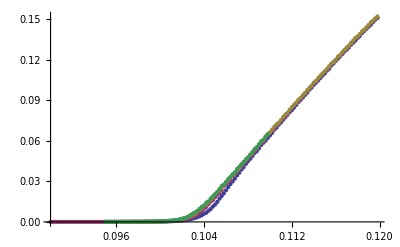

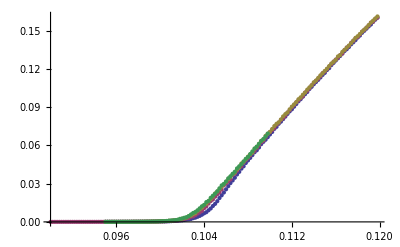

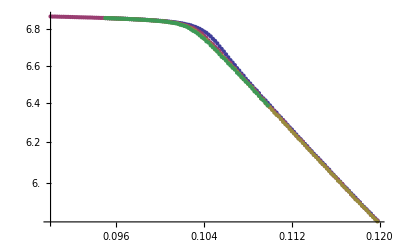

```mathematica
ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v7=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v7=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v7=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v7=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v7=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v7=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v7=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v7=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v7=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v7=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v7=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v7=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];



ListPlot[{gap5v7,gap10v7,gap20v7,gap30v7},PlotRange->Full]
ListPlot[{vel5v7,vel10v7,vel20v7,vel30v7}]
ListLogPlot[{avel5v7,avel10v7,avel20v7,avel30v7}]
```

```mathematica
gap1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gap1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10k1]}];
gap1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10k1]}];
gap1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10k1]}];
gap1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10k1]}];
gap1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g10k1]}];
gap1006=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g10k1]}];
gap1007=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g10k1]}];
```

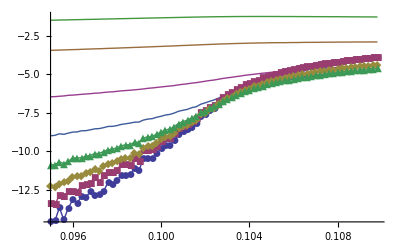

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007},PlotLegend->{"0","1","2","3","4","5","6","7"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full,PlotLabel->"GapDistribution, Vmax=7, 30k"]
```